```mathematica
hm=ColorNegate@Binarize@ImageResize[Import[NotebookDirectory[]<>"hammer.jpg"],{500,500}];
```

```mathematica
skills=({{Style["C++",Italic], 9}, {Style["Mathematica",Italic], 10}, {"Matlab", 9}, {"Shell Scripts", 6}, {"JavaScript", 4}, {"Python", 5}, {"Maple", 5}, {"CUDA", 7}, {"LaTeX", 7}, {"SQL", 5}, {"Git", 6}, {"Photography", 8}, {"AutoCAD", 4}, {"3D Printer", 5}, {"Machine Shop", 5}, {"Data Analysis", 8}, {"Machine Learning", 6}, {"Java", 5}, {"HTML", 5}, {"Digital Media", 7}, {"Algorithm", 6}, {"MPI", 5}, {"Visualization", 7}});skills[[;;,2]]=√skills[[;;,2]]+5;

(*g=WordCloud[skills,ColorNegate@Graphics[Rectangle[{0,0},{2,3}]], WordSpacings->4,ColorFunction->ColorData["Rainbow"],WordOrientation->{{0,Pi/30,-Pi/30}}, ImageSize->1000,Background->None]*)
```

```mathematica
Export[NotebookDirectory[]<>"wordCloud.png",Rasterize[g,Background->None,RasterSize->4000,ImageSize->1000],"PNG"]
```

/Users/b2l/GitHub/borntoleave.github.io/wordCloud.png

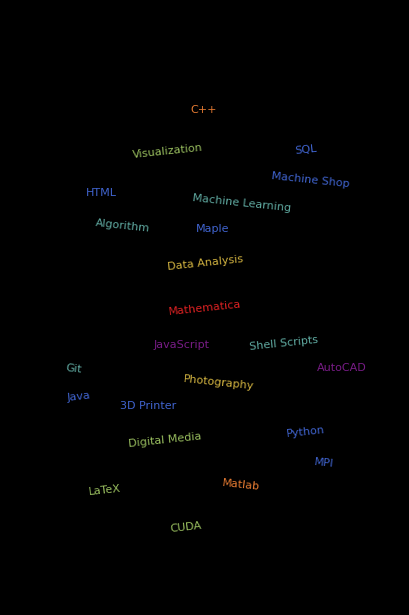

```mathematica
g=WordCloud[skills,ColorNegate@Graphics[Rectangle[{0,0},{2,3}]], WordSpacings->4,ColorFunction->ColorData["Rainbow"],WordOrientation->{{0,Pi/30,-Pi/30}},Background->None]
```